```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
Off[RowReduce::luc]
Off[Solve::svars]
$Assumptions={θ>0,n∈Integers,m∈Integers,j∈Integers,i∈Integers,n≥0,m≥0,j≥0,i≥0};
SetOptions[Plot,
PlotStyle->{{Red,Thick},{Purple,Thick},{Blue,Thick},{Cyan,Thick}},
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

colorlist={Blue,Red,Darker[Green],Darker[Yellow],Orange,Lighter[Green],Lighter[Brown],Purple,Cyan}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WriteDirectory="/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files/Optimal_Error_1D_Heat";
WriteDirectoryResults = "/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/";
SetDirectory[NotebookDirectory[]];
```

## Some Testing with Hermite Functions (normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];

(*Distribution with respect to L2*)
H2[i_,c_]=(1 2^(1/4) (2π)^(1/4))/(√Gamma[i+1] 2^(i/2))HermiteH[i,c];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];
fL2[c_,n_]:=∑_(k=0)^(n-1) α[k]H2[k,c]f0[c];

(*The following routine integrates the following expressions ∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc *)
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];

(*Simplified expression for half space integral *)
ExplicitHSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(m!))/(√(n!))(∑_(p=1)^n 1/((p-m-2)!! (1-p+m)! (p-n-1)!!)+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

## Equations for α_j, incl. Eigenvalues

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)

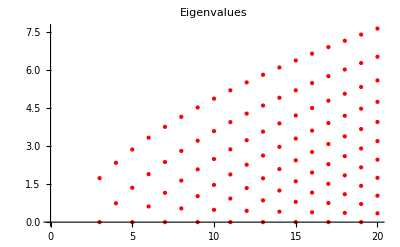

```mathematica
AA[n_]:=Table[If[i==j+1,√i,If[i==j-1,√(i+1),0]],{i,0,n-1},{j,0,n-1}]

MatrixForm[AA[4]]
ListPlot[N[Table[Thread[{Table[n,{i,1,If[OddQ[n],(n)/2+1,(n)/2]}],N[Select[Eigenvalues[AA[n]],#≥0&]]}],{n,3,20}]],PlotLabel->"Eigenvalues",PlotStyle->{{Red,Thick,PointSize[Large]}}]
```

## Boundary Matrices

```mathematica
Clear[MatBoe]
```

### Mat Aoe

```mathematica
(*construct Aoe*)
MatAoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];
Do[Do[If[ii==jj,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧],If[jj==ii+1,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧+1]]],{jj,1,Length[IDEven]}],{ii,1,Length[IDOdd]}];

result

]
```

### Mat Boe

```mathematica
(*With the assumption that the normal points from the gas into the wall.*)
MatBoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];


(*First we compute the density at the wall*)
rhoW=Expand[ρW/.Solve[(Expand[(ρW HSpcInt[1,0]+0 HSpcInt[1,1]+θW/√2 HSpcInt[1,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[1,2j]])==0,ρW]⟦1⟧];


(*2 comes from the left hand side of the boundary conditions and the minus comes from the direction of the normal*)
Do[result⟦ii⟧=-2((rhoW HSpcInt[IDOdd⟦ii⟧,0]+0 HSpcInt[IDOdd⟦ii⟧,1]+θW/√2 HSpcInt[IDOdd⟦ii⟧,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]
```

### Mat Onsager

```mathematica
MatOnsager[n_]:=Module[{Btilde,result},

Btilde=MatBoe[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧;
Btilde.Inverse[MatAoe[n]⟦1;;-1,1;;Length[MatAoe[n]]⟧]
]
```

## Check Boundary Stability

### Stability Check

```mathematica
CheckBoundary[n_]:=Module[{entropy,error,numEntries,OnsagerMat},

OnsagerMat =MatOnsager[n];
error =Simplify[ OnsagerMat-Transpose[OnsagerMat]];
numEntries=Length[Flatten[OnsagerMat]];

Print[Style["Num Tensors: ",FontColor->Black],n];
Print[Style["Checking Symmetricity",FontColor->Magenta]];
If[Count[Flatten[error],0]==numEntries,Print[Style["Symmetric",FontColor->Green]],Print[Style["UnSymmetric",FontColor->Red]]];

Print[Style["Checking Eigenvalues",FontColor->Brown]];
(*equality with zero will exists because of no penetration boundary condition*)
If[Length[Select[Eigenvalues[OnsagerMat],#<0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];

]
```

```mathematica
Ntensors = Range[4,20,1];
Do[CheckBoundary[ii],{ii,Ntensors}];
```

Num Tensors: 4

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 5

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 6

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 7

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 8

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 9

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 10

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 11

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 12

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 13

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 14

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 15

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 16

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 17

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 18

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 19

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 20

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

## Construct Boundary Conditions

### core routine

```mathematica
(*flag == 0 for unstable,flag == 1 for stable*)
ConstructStableBC[n_,flag_,Onsager_]:=Module[{BCMat,OddVar,EvenVar,IDEven,IDOdd,result,Boe},


IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];
result=Flatten[ConstantArray[0,{Length[IDOdd]-1}]];

OddVar=Map[α[#]&,IDOdd];
EvenVar=Map[α[#]&,IDEven];

If[flag==0,Boe=MatBoe[n],Boe=Onsager.MatAoe[n];];

(*we neglect the first boundary condition*)
Do[result⟦ii⟧=α[IDOdd⟦ii+1⟧]-Boe⟦ii+1,All⟧.Map[α[#]&,IDEven]+Boe⟦ii+1,2⟧/(√2)θW,{ii,1,Length[IDOdd]-1}];

Expand[Simplify[result]]
]
```

```mathematica
(*Do[bc0[ii]=ConstructStableBC[ii,0];
bc0Stable[ii]=ConstructStableBC[ii,1];,{ii,5,50}];*)
```

```mathematica
AA[5]//MatrixForm
```

(0 | 1 | 0 | 0 | 0
1 | 0 | √2 | 0 | 0
0 | √2 | 0 | √3 | 0
0 | 0 | √3 | 0 | 2
0 | 0 | 0 | 2 | 0)

```mathematica
Clear[bc]
```

### Acceptable Onsager Matrices

```mathematica
FixOnsager[OnsagerMat_]:=Module[{domain,OnsagerNew,ev,PositiveEV,commonelem},
OnsagerNew=OnsagerMat;
(*We only change the first two onsager coefficients*)

OnsagerNew⟦2,2⟧*=ζ1;
OnsagerNew⟦3,3⟧*=ζ2;

domain=Range[0.5,3,0.1];
domain=Flatten[Table[Table[{domain⟦ii⟧,domain⟦jj⟧},{jj,1,Length[domain]}],{ii,1,Length[domain]}],1];

(*list of eigenvalues corresponding to different values of the onsager coefficients*)
ev=Table[N[Eigenvalues[OnsagerNew⟦2;;-1,2;;-1⟧/.{ζ1->domain⟦ii,1⟧,ζ2->domain⟦ii,2⟧}]],{ii,1,Length[domain]}];

(*location of positive eigenvalues*)
PositiveEV=Table[Flatten[Position[ev⟦All,ii⟧,_?(#>0&)]],{ii,1,Length[ev⟦1⟧]}];
commonelem=PositiveEV⟦1⟧;
Do[commonelem=Intersection[PositiveEV⟦ii⟧,commonelem];,{ii,2,Length[PositiveEV]}];

{domain⟦commonelem⟧,ev⟦commonelem⟧,Table[OnsagerNew/.{ζ1->domain⟦commonelem⟦ii⟧,1⟧,ζ2->domain⟦commonelem⟦ii⟧,2⟧},{ii,1,Length[commonelem]}]}
]
```

### Test Range of Positivity

```mathematica
positiveEV=Table[FixOnsager[MatOnsager[ii]]⟦2⟧,{ii,7,23,2}];
```

```mathematica
Do[If[Length[Flatten[Position[positiveEV⟦ii⟧,_?(#<0&)]]]>0,Print[Style["Not Passed",FontColor->Red]],Print[Style["Passed",FontColor->Green]]];,{ii,1,Length[positiveEV]}]
```

Passed

Passed

Passed

«6 more identical outputs»

### OnsagerMatrices

```mathematica
min=6;
max=20;
```

```mathematica
(*The original onsager coefficients*)
Do[onsagerOld[ii]=MatOnsager[ii],{ii,min,max}];
```

```mathematica
(*onsager matrices which have positivity and symmetricity*)
(*Do[{onsagercoeff[ii],onsagerNew[ii]}=FixOnsager[onsagerOld[ii]]⟦{1,-1}⟧,{ii,min,max}];*)
```

$Aborted

### Boundary Conditions

```mathematica
(*Do[bcPBCOptimal[ii]=Table[ConstructStableBC[ii,1,onsagerNew[ii]⟦jj⟧],{jj,1,Length[onsagerNew[ii]]}],{ii,min,max}];*)

Do[bcMBC[ii]=ConstructStableBC[ii,0,onsagerOld[ii]],{ii,min,max}];

Do[bcPBC[ii]=ConstructStableBC[ii,1,onsagerOld[ii]],{ii,min,max}];
```

## Solving Routines

### returns the solution

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

(*flag = 0 for unstable, flag == 1 for stable*)
GetSolution[nvar_,kn_,thetaw_,flag_,bcinput_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦1⟧=0;
alpha=0;

coef[0,4]=Kn k[0]; (* heat flux constant*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];
res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


bc=bcinput;

bcEqn=Table[bc⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

(*Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}*)
{{√2. α[2],√6. α[3]}/.res/.solBC/.{Kn->kn},Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}}
]
```

```mathematica
(*u[x_]=GetSolution[4,0.1,1.0]
Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]]/.{Kn->0.1}]]
*)
```

### returns the distribution function

```mathematica
(*flag = 0 for unstable, flag == 1 for stable*)
Getf[nvar_,kn_,thetaw_,flag_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc0,result},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦1⟧=0;
alpha=0;

coef[0,4]=Kn k[0]; (* heat flux constant*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];
res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


If[flag==0,bc0=ConstructStableBC[nvar,0],bc0=ConstructStableBC[nvar,1]];

bcEqn=Table[bc0⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

(*Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}*)

res/.solBC/.{Kn->kn}
]
```

## Acceleration

### Accelerate series expansion

```mathematica
(*gives the output of accelerated series*)
CreateAcc[list_]:=Module[{size,Sn,result},
size = Length[list];

(*binomial series corresponding to each term*)
Sn = ConstantArray[0,size];
Do[Sn⟦ii⟧=Sum[(-1)^(jj-1)Binomial[ii-1,jj-1]list⟦ii-jj+1⟧,{jj,1,ii}],{ii,1,size}];

result = Sum[(-1)^(ii-1)Sn⟦ii⟧/2^ii,{ii,1,size}]
]
```

#### coeffs of a_k

```mathematica
(*in the following routine we compute the coefficients of Subscript[a, k]
N = total terms-1, r = k*)
Coeffak[N_,r_]:=(-1)^r Sum[Binomial[N-j,N-r-j]/2^(N-j+1),{j,0,N-r}];
```

#### Averaging factor

```mathematica
(*the following is the factor which should be used while averagin the final result of the accelerated series*)
CoeffAvg[N_]:=Sum[Abs[Coeffak[N,r]],{r,0,N}];
```

### Accelerated solution

```mathematica
AccSolution[list_]:=Module[{ak,AccSol},
ak = Table[(-1)^(ii-1)list⟦ii⟧,{ii,1,Length[list]}];
AccSol = CreateAcc[ak]/CoeffAvg[Length[list]-1];
AccSol
]
```

## Discrete Velocity Solution

```mathematica
Arrayθ[gaussloc_,gaussW_]:=Table[gaussW⟦ii⟧(gaussloc⟦ii⟧^2-1),{ii,1,Length[gaussW]}];
```

### Kn 0.1

```mathematica
exactfKn0p1=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn0p1/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn0p1=exactfKn0p1⟦1,IDpointsc⟧;
pointsxKn0p1=exactfKn0p1⟦1,IDpointsx⟧;
θKn0p1=Interpolation[Table[{exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,2⟧,exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,3⟧].exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,4⟧},{ii,1,pointsxKn0p1}],InterpolationOrder->3];

fKn0p1=Table[Interpolation[Table[{exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+jj,2⟧,exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn0p1}],InterpolationOrder->3],{ii,1,pointsxKn0p1}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

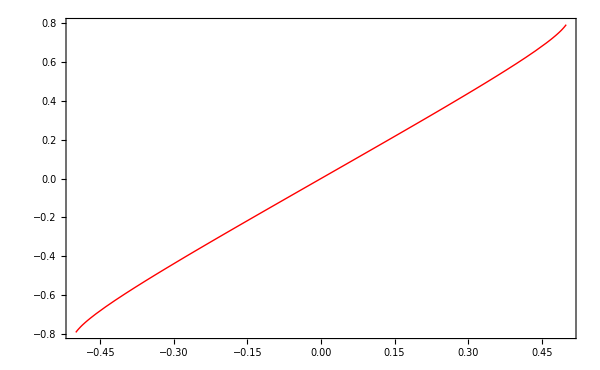

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

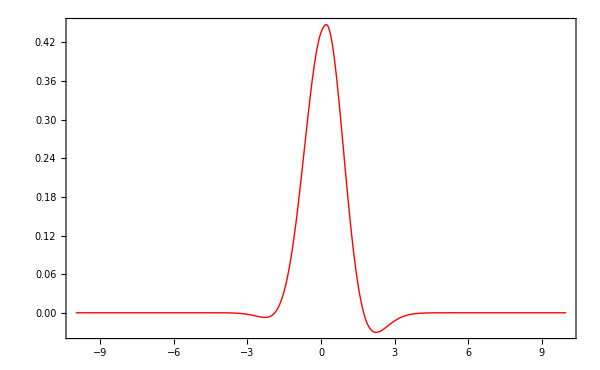

```mathematica
Plot[{θKn0p1[x]},{x,-0.5,0.5}]
Plot[{fKn0p1⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 1.0

```mathematica
exactfKn1p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn1p0/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn1p0=exactfKn1p0⟦1,IDpointsc⟧;
pointsxKn1p0=exactfKn1p0⟦1,IDpointsx⟧;
θKn1p0=Interpolation[Table[{exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,2⟧,exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,3⟧].exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,4⟧},{ii,1,pointsxKn1p0}],InterpolationOrder->3];

fKn1p0=Table[Interpolation[Table[{exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+jj,2⟧,exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn1p0}],InterpolationOrder->3],{ii,1,pointsxKn1p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

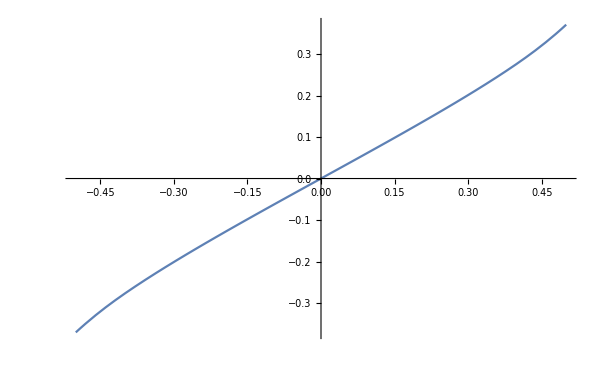

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

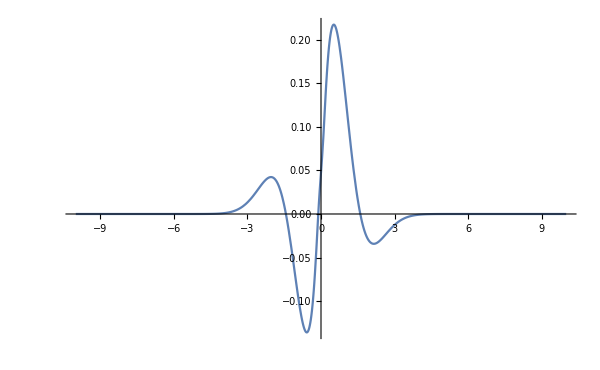

```mathematica
Plot[{θKn1p0[x]},{x,-0.5,0.5}]
Plot[{fKn1p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 10.0

```mathematica
exactfKn10p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn10p0/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn10p0=exactfKn10p0⟦1,IDpointsc⟧;
pointsxKn10p0=exactfKn10p0⟦1,IDpointsx⟧;
θKn10p0=Interpolation[Table[{exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,2⟧,exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,3⟧].exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,4⟧},{ii,1,pointsxKn10p0}],InterpolationOrder->3];

fKn10p0=Table[Interpolation[Table[{exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+jj,2⟧,exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn10p0}],InterpolationOrder->3],{ii,1,pointsxKn10p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

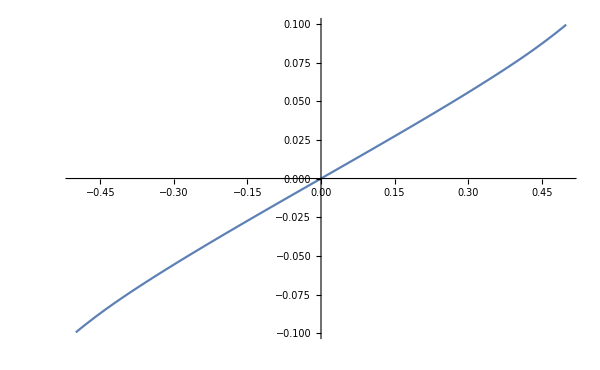

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

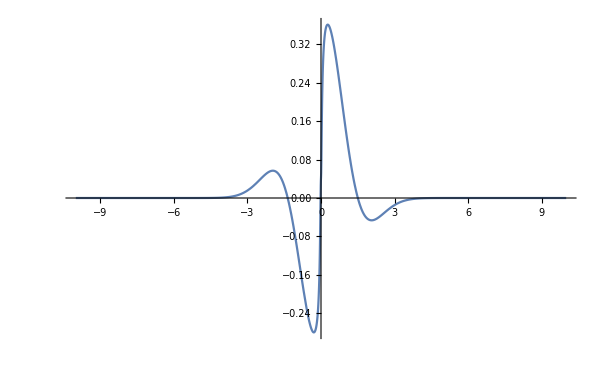

```mathematica
Plot[{θKn10p0[x]},{x,-0.5,0.5}]
Plot[{fKn10p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 100.0

```mathematica
exactfKn100p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn100p0/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn100p0=exactfKn100p0⟦1,IDpointsc⟧;
pointsxKn100p0=exactfKn100p0⟦1,IDpointsx⟧;
θKn100p0=Interpolation[Table[{exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,2⟧,exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,3⟧].exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,4⟧},{ii,1,pointsxKn100p0}],InterpolationOrder->3];

fKn100p0=Table[Interpolation[Table[{exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+jj,2⟧,exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn100p0}],InterpolationOrder->3],{ii,1,pointsxKn100p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

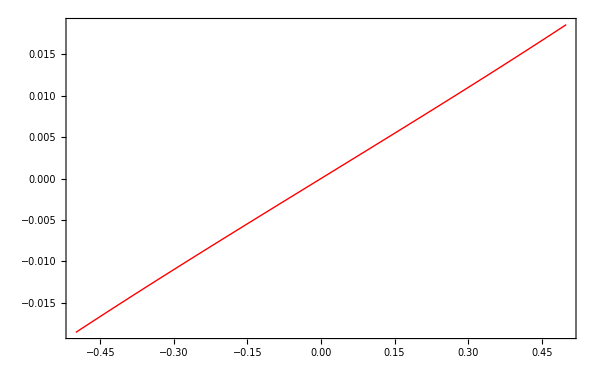

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

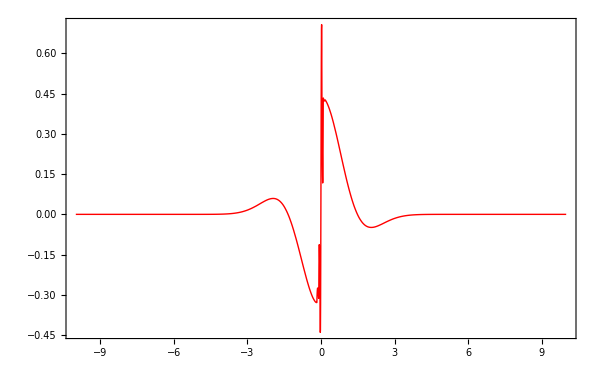

```mathematica
Plot[{θKn100p0[x]},{x,-0.5,0.5}]
Plot[{fKn100p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn ∞

```mathematica
exactfKn∞=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kninf/fx9c160.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn∞=exactfKn∞⟦1,IDpointsc⟧;
pointsxKn∞=exactfKn∞⟦1,IDpointsx⟧;
θKn∞=Interpolation[Table[{exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,2⟧,exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,3⟧].exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,4⟧},{ii,1,pointsxKn∞}],InterpolationOrder->3];

fKn∞=Table[Interpolation[Table[{exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+jj,2⟧,exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn∞}],InterpolationOrder->3],{ii,1,pointsxKn∞}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

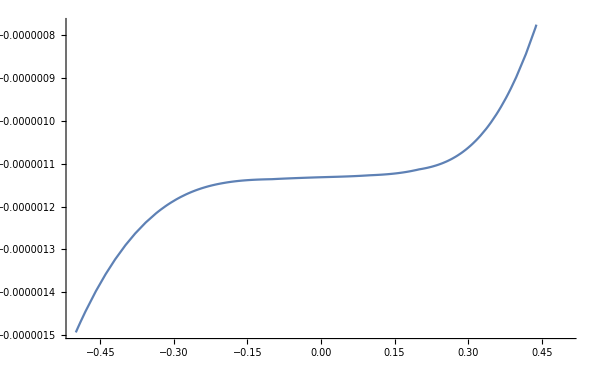

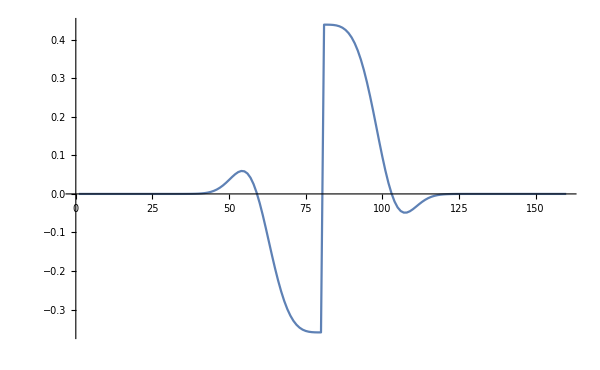

```mathematica
Plot[{Chop[θKn∞[x],10^-7]},{x,-0.5,0.5}]
ListPlot[exactfKn∞⟦IDdata+1;;IDdata+pointscKn∞,4⟧,PlotRange->Full,Joined->True]
```

## High Order Moment (Reference)

```mathematica
VarRef = 70;
```

```mathematica
OnsagerRef = MatOnsager[70];
bcRef=ConstructStableBC[70,0,OnsagerRef];
```

### Kn 0.1

```mathematica
HighOrderKn0p1[x_] = GetSolution[VarRef,0.1,1.0,1,bcRef]⟦1,1⟧;
```

### Kn 1.0

```mathematica
HighOrderKn1p0[x_] = GetSolution[VarRef,1.0,1.0,1,bcRef]⟦1,1⟧;
```

### Kn 10.0

```mathematica
HighOrderKn10p0[x_] = GetSolution[VarRef,10.0,1.0,1,bcRef]⟦1,1⟧;
```

### Kn 100.0

```mathematica
HighOrderKn100p0[x_] = GetSolution[VarRef,100.0,1.0,1,bcRef]⟦1,1⟧;
```

## Return Error

```mathematica
(*Returns the error. Flag == 0 for MBC, Flag == 1 for PBC and Flag == 2 for PBCOptimal*)
ReturnError[nvar_,Kn_,flag_,ref_]:=Module[{onsagerMat,bc,solution,error,numsolutions,time1,time2,gaussx,gaussW,domain},

If[nvar <min || nvar >max,Print[Style["Variables beyond present theory",FontColor->Red]]];

Which[flag==0,
bc={bcMBC[nvar]};,
flag==1,
bc={bcPBC[nvar]};,
flag==2,
Print[Style["Not Implemented",FontColor->Red]];
bc=bcPBCOptimal[nvar];];

numsolutions=Length[bc];

time1=AbsoluteTiming[Do[
solution[ii][x_]=GetSolution[nvar,Kn,1.0,1,bc⟦ii⟧]⟦1,1⟧;,{ii,1,numsolutions}]];

gaussx=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,1⟧;
gaussW=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,2⟧;

time2=AbsoluteTiming[Which[Kn==0.1,
error=Table[Sum[gaussW⟦jj⟧Abs[(solution[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,1,numsolutions}];,
Kn==1.0,
error=Table[Sum[gaussW⟦jj⟧Abs[(solution[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,1,numsolutions}];,
Kn==10.0,
error=Table[Sum[gaussW⟦jj⟧Abs[(solution[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,1,numsolutions}];,
Kn==100.0,
error=Table[Sum[gaussW⟦jj⟧Abs[(solution[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,1,numsolutions}];
]];

Print["Time in solving ",time1];
Print["Time in error computation ",time2];
{Flatten[Position[error,Min[error]]],Min[error],error}

]

(*returns the error corresponding to averaged solution *)
ReturnErrorAvg[min_,max_,Kn_,ref_]:=Module[{solution,solutionAvg,bc,gaussW,gaussx,error},

(*loop over all the possible nvars *)
Do[bc= bcPBC[ii];
solution[ii][x_]=GetSolution[ii,Kn,1.0,1,bc]⟦1,1⟧;,{ii,min,max}];

Print[Style["Obtained solution",FontColor->Cyan]];

Do[solutionAvg[ii][x_]=Mean[Table[solution[jj][x],{jj,min,ii}]],{ii,min,max}];

gaussx=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,1⟧;
gaussW=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,2⟧;


Which[Kn==0.1,
Print[Style["Computing error for Kn = 0.1",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==1.0,
Print[Style["Computing error for Kn = 1.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==10.0,
Print[Style["Computing error for Kn = 10.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==100.0,
Print[Style["Computing error for Kn = 100.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];
];

error
]

(*Error from accelerated series expansion*)
ReturnErrorAcc[min_,max_,Kn_,ref_]:=Module[{solution,solutionAvg,bc,gaussW,gaussx,error},

(*loop over all the possible nvars *)
Do[bc= bcPBC[ii];
solution[ii][x_]=GetSolution[ii,Kn,1.0,1,bc]⟦1,1⟧;,{ii,min,max}];

Print[Style["Obtained solution",FontColor->Cyan]];

Do[solutionAvg[ii][x_]=AccSolution[Table[solution[jj][x],{jj,min,ii}]],{ii,min,max}];

gaussx=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,1⟧;
gaussW=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,2⟧;


Which[Kn==0.1,
Print[Style["Computing error for Kn = 0.1",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==1.0,
Print[Style["Computing error for Kn = 1.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==10.0,
Print[Style["Computing error for Kn = 10.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==100.0,
Print[Style["Computing error for Kn = 100.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];
];

error
]
```

## Results

### Writting routine

```mathematica
WriteError[result_,filename_,Ntensors_]:=Module[{str},

str=OpenWrite[StringJoin[WriteDirectory,"/",filename,ToString[Ntensors],".dat"]];

(*Write the number of tensors and the optimal error value*)
WriteString[str," Tensors ",ToString[Ntensors]," Optimal Error ",result⟦2⟧,"\n"];
WriteString[str," #error","\n"];

Do[WriteString[str,ToString[result⟦3⟧⟦ii⟧],"\n"];,{ii,1,Length[result⟦3⟧]}];

Close[str];
]
```

### MBC

#### Kn = 0.1

```mathematica
Do[resultMBCKn0p1[ii]=ReturnError[ii,0.1,0,HighOrderKn0p1]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00818,Null}

Time in error computation {0.00163,Null}

Time in solving {0.01184,Null}

Time in error computation {0.00197,Null}

Time in solving {0.01047,Null}

Time in error computation {0.0017,Null}

Time in solving {0.01234,Null}

Time in error computation {0.00178,Null}

Time in solving {0.01631,Null}

Time in error computation {0.00178,Null}

Time in solving {0.02008,Null}

Time in error computation {0.00179,Null}

Time in solving {0.02557,Null}

Time in error computation {0.00183,Null}

Time in solving {0.02853,Null}

Time in error computation {0.00186,Null}

Time in solving {0.04083,Null}

Time in error computation {0.00223,Null}

Time in solving {0.04743,Null}

Time in error computation {0.00214,Null}

Time in solving {0.06705,Null}

Time in error computation {0.00288,Null}

Time in solving {0.06996,Null}

Time in error computation {0.00204,Null}

Time in solving {0.08257,Null}

Time in error computation {0.00228,Null}

Time in solving {0.09139,Null}

Time in error computation {0.0021,Null}

Time in solving {0.10834,Null}

Time in error computation {0.00266,Null}

#### Kn = 1.0

```mathematica
Do[resultMBCKn1p0[ii]=ReturnError[ii,1,0,HighOrderKn1p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.0064,Null}

Time in error computation {0.00178,Null}

Time in solving {0.00705,Null}

Time in error computation {0.00163,Null}

Time in solving {0.01086,Null}

Time in error computation {0.00183,Null}

Time in solving {0.01163,Null}

Time in error computation {0.00215,Null}

Time in solving {0.01603,Null}

Time in error computation {0.00177,Null}

Time in solving {0.02046,Null}

Time in error computation {0.00184,Null}

Time in solving {0.02542,Null}

Time in error computation {0.00187,Null}

Time in solving {0.03232,Null}

Time in error computation {0.00208,Null}

Time in solving {0.04409,Null}

Time in error computation {0.00236,Null}

Time in solving {0.04888,Null}

Time in error computation {0.00196,Null}

Time in solving {0.06743,Null}

Time in error computation {0.00204,Null}

Time in solving {0.07335,Null}

Time in error computation {0.00296,Null}

Time in solving {0.08699,Null}

Time in error computation {0.00213,Null}

Time in solving {0.1087,Null}

Time in error computation {0.0021,Null}

Time in solving {0.13214,Null}

Time in error computation {0.00235,Null}

#### Kn = 10.0

```mathematica
Do[resultMBCKn10p0[ii]=ReturnError[ii,10.0,0,HighOrderKn10p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00647,Null}

Time in error computation {0.00248,Null}

Time in solving {0.00663,Null}

Time in error computation {0.00211,Null}

Time in solving {0.01063,Null}

Time in error computation {0.0017,Null}

Time in solving {0.0147,Null}

Time in error computation {0.00283,Null}

Time in solving {0.01742,Null}

Time in error computation {0.00176,Null}

Time in solving {0.01917,Null}

Time in error computation {0.00173,Null}

Time in solving {0.02659,Null}

Time in error computation {0.00183,Null}

Time in solving {0.03031,Null}

Time in error computation {0.00199,Null}

Time in solving {0.03997,Null}

Time in error computation {0.00187,Null}

Time in solving {0.04295,Null}

Time in error computation {0.00216,Null}

Time in solving {0.05869,Null}

Time in error computation {0.0021,Null}

Time in solving {0.06734,Null}

Time in error computation {0.00277,Null}

Time in solving {0.08951,Null}

Time in error computation {0.00213,Null}

Time in solving {0.10147,Null}

Time in error computation {0.00364,Null}

Time in solving {0.12668,Null}

Time in error computation {0.00233,Null}

#### Kn = 100.0

```mathematica
Do[resultMBCKn100p0[ii]=ReturnError[ii,100.0,0,HighOrderKn100p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00577,Null}

Time in error computation {0.00179,Null}

Time in solving {0.00685,Null}

Time in error computation {0.00169,Null}

Time in solving {0.01151,Null}

Time in error computation {0.00162,Null}

Time in solving {0.01211,Null}

Time in error computation {0.00166,Null}

Time in solving {0.01664,Null}

Time in error computation {0.00171,Null}

Time in solving {0.01918,Null}

Time in error computation {0.00171,Null}

Time in solving {0.02516,Null}

Time in error computation {0.00181,Null}

Time in solving {0.0304,Null}

Time in error computation {0.0018,Null}

Time in solving {0.0378,Null}

Time in error computation {0.00187,Null}

Time in solving {0.04597,Null}

Time in error computation {0.00221,Null}

Time in solving {0.06265,Null}

Time in error computation {0.00405,Null}

Time in solving {0.09452,Null}

Time in error computation {0.00224,Null}

Time in solving {0.0877,Null}

Time in error computation {0.00229,Null}

Time in solving {0.10373,Null}

Time in error computation {0.00253,Null}

Time in solving {0.10931,Null}

Time in error computation {0.00212,Null}

### PBC

#### Kn = 0.1

```mathematica
Do[resultPBCKn0p1[ii]=ReturnError[ii,0.1,1,HighOrderKn0p1]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00928,Null}

Time in error computation {0.00352,Null}

Time in solving {0.01343,Null}

Time in error computation {0.00315,Null}

Time in solving {0.01319,Null}

Time in error computation {0.00263,Null}

Time in solving {0.01657,Null}

Time in error computation {0.00375,Null}

Time in solving {0.02975,Null}

Time in error computation {0.00347,Null}

Time in solving {0.03213,Null}

Time in error computation {0.0018,Null}

Time in solving {0.03714,Null}

Time in error computation {0.00188,Null}

Time in solving {0.05114,Null}

Time in error computation {0.00204,Null}

Time in solving {0.04051,Null}

Time in error computation {0.00197,Null}

Time in solving {0.06192,Null}

Time in error computation {0.00268,Null}

Time in solving {0.09133,Null}

Time in error computation {0.00446,Null}

Time in solving {0.09143,Null}

Time in error computation {0.00425,Null}

Time in solving {0.11796,Null}

Time in error computation {0.00212,Null}

Time in solving {0.09131,Null}

Time in error computation {0.00209,Null}

Time in solving {0.1195,Null}

Time in error computation {0.00266,Null}

#### Kn = 1.0

```mathematica
Do[resultPBCKn1p0[ii]=ReturnError[ii,1,1,HighOrderKn1p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00627,Null}

Time in error computation {0.00187,Null}

Time in solving {0.00614,Null}

Time in error computation {0.00171,Null}

Time in solving {0.01188,Null}

Time in error computation {0.00169,Null}

Time in solving {0.01332,Null}

Time in error computation {0.00168,Null}

Time in solving {0.01799,Null}

Time in error computation {0.00176,Null}

Time in solving {0.02176,Null}

Time in error computation {0.0019,Null}

Time in solving {0.02843,Null}

Time in error computation {0.00199,Null}

Time in solving {0.03232,Null}

Time in error computation {0.00197,Null}

Time in solving {0.04846,Null}

Time in error computation {0.00189,Null}

Time in solving {0.0471,Null}

Time in error computation {0.00217,Null}

Time in solving {0.06835,Null}

Time in error computation {0.00231,Null}

Time in solving {0.08303,Null}

Time in error computation {0.0028,Null}

Time in solving {0.099874,Null}

Time in error computation {0.00206,Null}

Time in solving {0.11461,Null}

Time in error computation {0.00245,Null}

Time in solving {0.13576,Null}

Time in error computation {0.00251,Null}

#### Kn = 10.0

```mathematica
Do[resultPBCKn10p0[ii]=ReturnError[ii,10.0,1,HighOrderKn10p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00711,Null}

Time in error computation {0.00182,Null}

Time in solving {0.00649,Null}

Time in error computation {0.00156,Null}

Time in solving {0.01094,Null}

Time in error computation {0.00187,Null}

Time in solving {0.01106,Null}

Time in error computation {0.00174,Null}

Time in solving {0.01573,Null}

Time in error computation {0.00189,Null}

Time in solving {0.02021,Null}

Time in error computation {0.00183,Null}

Time in solving {0.02627,Null}

Time in error computation {0.00191,Null}

Time in solving {0.02955,Null}

Time in error computation {0.00181,Null}

Time in solving {0.03855,Null}

Time in error computation {0.00195,Null}

Time in solving {0.04599,Null}

Time in error computation {0.00211,Null}

Time in solving {0.06044,Null}

Time in error computation {0.00207,Null}

Time in solving {0.07012,Null}

Time in error computation {0.00206,Null}

Time in solving {0.08705,Null}

Time in error computation {0.00282,Null}

Time in solving {0.097547,Null}

Time in error computation {0.00231,Null}

Time in solving {0.10751,Null}

Time in error computation {0.00209,Null}

#### Kn = 100.0

```mathematica
Do[resultPBCKn100p0[ii]=ReturnError[ii,100.0,1,HighOrderKn100p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00632,Null}

Time in error computation {0.00166,Null}

Time in solving {0.0103,Null}

Time in error computation {0.00157,Null}

Time in solving {0.01186,Null}

Time in error computation {0.00226,Null}

Time in solving {0.01225,Null}

Time in error computation {0.00166,Null}

Time in solving {0.01735,Null}

Time in error computation {0.00171,Null}

Time in solving {0.01946,Null}

Time in error computation {0.0017,Null}

Time in solving {0.02542,Null}

Time in error computation {0.0018,Null}

Time in solving {0.03071,Null}

Time in error computation {0.00177,Null}

Time in solving {0.03953,Null}

Time in error computation {0.00187,Null}

Time in solving {0.04555,Null}

Time in error computation {0.00208,Null}

Time in solving {0.06034,Null}

Time in error computation {0.00215,Null}

Time in solving {0.07308,Null}

Time in error computation {0.00292,Null}

Time in solving {0.08558,Null}

Time in error computation {0.00257,Null}

Time in solving {0.11085,Null}

Time in error computation {0.00215,Null}

Time in solving {0.11369,Null}

Time in error computation {0.00252,Null}

### PBC Optimal

#### Kn = 0.1

```mathematica
Do[resultPBCOptKn0p1[ii]=ReturnError[ii,0.1,2],{ii,min,max}];
```

Time in solving {3.32828,Null}

Time in error computation {0.56652,Null}

Time in solving {3.9554,Null}

Time in error computation {0.53099,Null}

Time in solving {6.03347,Null}

Time in error computation {0.62628,Null}

Time in solving {7.03237,Null}

Time in error computation {0.61596,Null}

Time in solving {9.967276,Null}

Time in error computation {0.66416,Null}

Time in solving {11.784,Null}

Time in error computation {0.69167,Null}

Time in solving {16.05214,Null}

Time in error computation {0.73663,Null}

Time in solving {18.38194,Null}

Time in error computation {0.74761,Null}

Time in solving {25.21315,Null}

Time in error computation {0.82303,Null}

Time in solving {27.89766,Null}

Time in error computation {0.81385,Null}

Time in solving {34.97629,Null}

Time in error computation {0.87265,Null}

Time in solving {39.26779,Null}

Time in error computation {0.87894,Null}

Time in solving {51.34053,Null}

Time in error computation {0.954113,Null}

Time in solving {54.3659,Null}

Time in error computation {1.01767,Null}

Time in solving {66.82811,Null}

Time in error computation {0.991743,Null}

#### Kn = 1.0

```mathematica
Do[resultPBCOptKn1p0[ii]=ReturnError[ii,1,2],{ii,min,max}];
```

Time in solving {3.5478,Null}

Time in error computation {0.60438,Null}

Time in solving {4.05621,Null}

Time in error computation {0.57063,Null}

Time in solving {6.36971,Null}

Time in error computation {0.63444,Null}

Time in solving {7.47429,Null}

Time in error computation {0.66669,Null}

Time in solving {10.63213,Null}

Time in error computation {0.741,Null}

Time in solving {12.35224,Null}

Time in error computation {0.71107,Null}

Time in solving {17.46853,Null}

Time in error computation {0.822,Null}

Time in solving {20.20483,Null}

Time in error computation {0.78974,Null}

Time in solving {26.52482,Null}

Time in error computation {0.87077,Null}

Time in solving {30.07518,Null}

Time in error computation {0.88313,Null}

Time in solving {40.30607,Null}

Time in error computation {0.88556,Null}

Time in solving {41.97718,Null}

Time in error computation {0.989031,Null}

Time in solving {54.50316,Null}

Time in error computation {1.03564,Null}

Time in solving {10855.94126,Null}

Time in error computation {0.94917,Null}

Time in solving {59650.80097,Null}

Time in error computation {1.81326,Null}

#### Kn = 10.0

```mathematica
Do[resultPBCOptKn10p0[ii][x_]=ReturnError[ii,10.0,2],{ii,min,max}];
```

Time in solving {3.98041,Null}

Time in error computation {0.57475,Null}

Time in solving {5.25406,Null}

Time in error computation {0.59576,Null}

Time in solving {7.99848,Null}

Time in error computation {0.76367,Null}

Time in solving {8.12211,Null}

Time in error computation {0.73336,Null}

Time in solving {12.5387,Null}

Time in error computation {0.87907,Null}

Time in solving {13.6071,Null}

Time in error computation {0.69977,Null}

Time in solving {19.524,Null}

Time in error computation {1.05253,Null}

Time in solving {19.88695,Null}

Time in error computation {0.74015,Null}

$Aborted

### Plots

#### Kn = 0.1

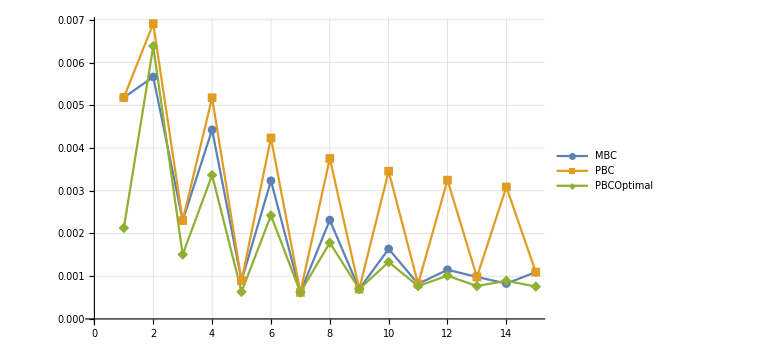

```mathematica
ListPlot[{Table[resultMBCKn0p1[ii],{ii,min,max}],Table[resultPBCKn0p1[ii],{ii,min,max}],Table[resultPBCOptKn0p1[ii]⟦2⟧,{ii,min,max}]},Joined->True,PlotLegends->{"MBC","PBC","PBCOptimal"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

#### Kn = 1.0

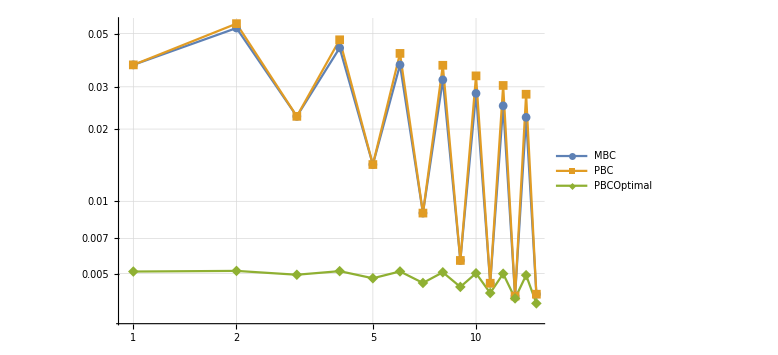

```mathematica
ListLogLogPlot[{Table[resultMBCKn1p0[ii],{ii,min,max}],Table[resultPBCKn1p0[ii],{ii,min,max}],Table[resultPBCOptKn1p0[ii]⟦2⟧,{ii,min,max}]},Joined->True,PlotLegends->{"MBC","PBC","PBCOptimal"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

#### Kn = 10.0

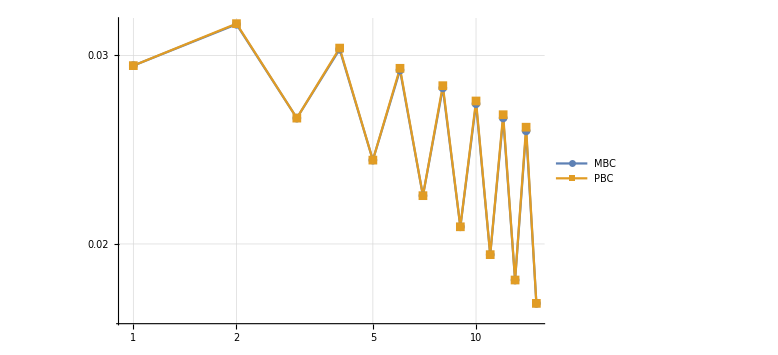

```mathematica
ListLogLogPlot[{Table[resultMBCKn10p0[ii][x],{ii,min,max}],Table[resultPBCKn10p0[ii][x],{ii,min,max}](*,Table[resultPBCOptKn10p0[ii][x]⟦2⟧,{ii,min,max}]*)},Joined->True,PlotLegends->{"MBC","PBC","PBCOptimal"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

### Plots for paper

#### plotting routine

```mathematica
PlotError[error_,Kn_]:=Module[{numvariations,ptlegends,TicksXAxis,legendfont},

(*Number of variations which we allow in the plot*)
numvariations=Length[error];
If[numvariations==1,Print[Style["Not Implemeneted",FontColor->Red]]];

legendfont = 16;
Which[numvariations==2,
ptlegends={Style["MBC",FontSize->legendfont],Style["WPBC",FontSize->legendfont]},
numvariations==3,
ptlegends={Style["MBC",FontSize->legendfont],Style["WPBC",FontSize->legendfont],Style["WPBC-Optimal",FontSize->legendfont]}];

TicksXAxis = Table[{ii-min+1,ii},{ii,min,max,1}];

ListPlot[error,Frame->True,GridLines->Automatic,FrameLabel->{{Style["errorθ",FontSize->16],None},{Style["m",FontSize->16],None}},FrameTicks->{{Automatic,None},{TicksXAxis,None}},ImageSize->600,Joined->True,PlotMarkers->{Graphics[{Red,Thick,Circle[]},ImageSize->14],Graphics[{Green,Thick,Circle[]},ImageSize->10]},PlotStyle->{{Red,Thick},{Green,Thick}},PlotLegends->Placed[{ptlegends},{0.8,0.9}],FrameTicksStyle->{{Directive[FontSize->13,Black],None},{Directive[FontSize->13,{Orange,Black}],None}}]

]
```

#### Kn = 0.1

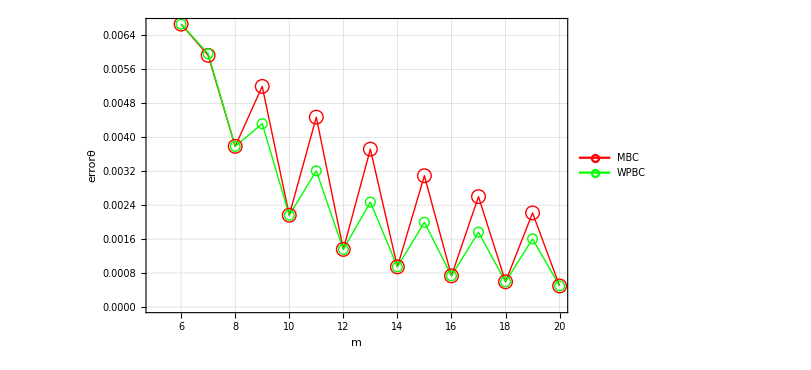

```mathematica
ptKn0p1=PlotError[{Table[resultMBCKn0p1[ii],{ii,min,max}],Table[resultPBCKn0p1[ii],{ii,min,max}]},0.1]
```

```mathematica
Export[StringJoin[WriteDirectoryResults,"Physical_Accuracy/Kn0p1/","error_theta.eps"],ptKn0p1]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Physical_Accuracy/Kn0p1/error_theta.eps

#### Kn = 1.0

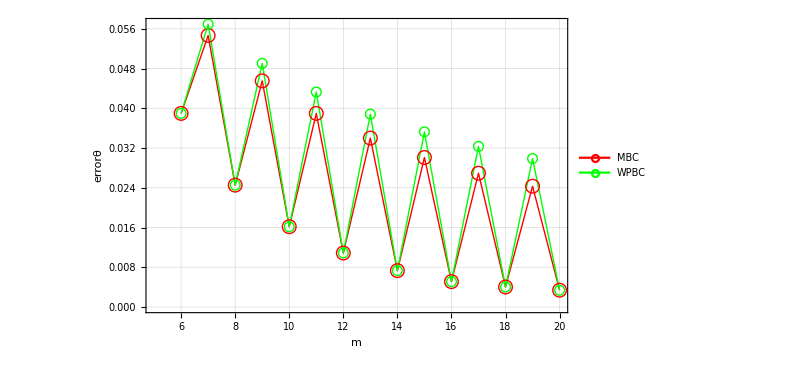

```mathematica
ptKn1p0=PlotError[{Table[resultMBCKn1p0[ii],{ii,min,max}],Table[resultPBCKn1p0[ii],{ii,min,max}]},0.1]
```

```mathematica
Export[StringJoin[WriteDirectoryResults,"/Kn1p0/","error_theta.eps"],ptKn1p0]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Physical_Accuracy/Kn1p0/error_theta.eps

#### Kn = 10.0

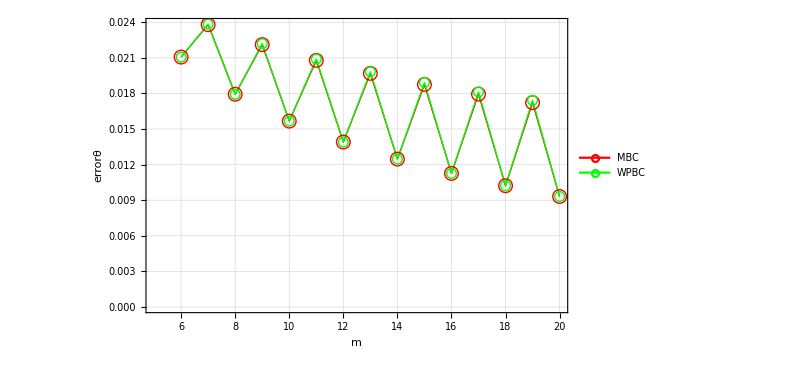

```mathematica
ptKn10p0=PlotError[{Table[resultMBCKn10p0[ii],{ii,min,max}],Table[resultPBCKn10p0[ii],{ii,min,max}]},0.1]
```

```mathematica
Export[StringJoin[WriteDirectoryResults,"/Kn10p0/","error_theta.eps"],ptKn10p0]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Physical_Accuracy/Kn10p0/error_theta.eps

### Error variation for different theories

#### Ntensors = 7

```mathematica
error7Kn0p1=ReturnError[7,0.1,2]⟦-1⟧;
error7Kn1p0=ReturnError[7,1.0,2]⟦-1⟧;
error7Kn10p0=ReturnError[7,10.0,2]⟦-1⟧;
error7Kn0p1=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error7Kn0p1⟦ii⟧}],{ii,1,Length[error7Kn0p1]}];
error7Kn1p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error7Kn1p0⟦ii⟧}],{ii,1,Length[error7Kn1p0]}];
error7Kn10p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error7Kn10p0⟦ii⟧}],{ii,1,Length[error7Kn10p0]}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {4.11116,Null}

Time in error computation {0.6499,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {4.30056,Null}

Time in error computation {0.78213,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {4.31841,Null}

Time in error computation {0.66279,Null}

```mathematica
ListPlot3D[error7Kn0p1]
ListPlot3D[error7Kn1p0]
ListPlot3D[error7Kn10p0]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

#### Ntensors = 8

```mathematica
error8Kn0p1=ReturnError[8,0.1,2]⟦-1⟧;
error8Kn1p0=ReturnError[8,1.0,2]⟦-1⟧;
error8Kn10p0=ReturnError[8,10.0,2]⟦-1⟧;
error8Kn0p1=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error8Kn0p1⟦ii⟧}],{ii,1,Length[error8Kn0p1]}];
error8Kn1p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error8Kn1p0⟦ii⟧}],{ii,1,Length[error8Kn1p0]}];
error8Kn10p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error8Kn10p0⟦ii⟧}],{ii,1,Length[error8Kn10p0]}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {6.31555,Null}

Time in error computation {0.72682,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {6.20566,Null}

Time in error computation {0.72142,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {6.17609,Null}

Time in error computation {0.70443,Null}

```mathematica
ListPlot3D[error8Kn0p1]
ListPlot3D[error8Kn1p0]
ListPlot3D[error8Kn10p0]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

#### Ntensors = 9

```mathematica
error9Kn0p1=ReturnError[9,0.1,2]⟦-1⟧;
error9Kn1p0=ReturnError[9,1.0,2]⟦-1⟧;
error9Kn10p0=ReturnError[9,10.0,2]⟦-1⟧;
error9Kn0p1=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error9Kn0p1⟦ii⟧}],{ii,1,Length[error9Kn0p1]}];
error9Kn1p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error9Kn1p0⟦ii⟧}],{ii,1,Length[error9Kn1p0]}];
error9Kn10p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error9Kn10p0⟦ii⟧}],{ii,1,Length[error9Kn10p0]}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {7.472,Null}

Time in error computation {0.751,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {7.31988,Null}

Time in error computation {0.71083,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {7.29556,Null}

Time in error computation {0.71168,Null}

```mathematica
ListPlot3D[error9Kn0p1]
ListPlot3D[error9Kn1p0]
ListPlot3D[error9Kn10p0]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

### Value Optimal Onsager Coefficients

```mathematica
OptimalCoeffsKn0p1=Table[onsagercoeff[ii]⟦resultPBCOptKn0p1[ii]⟦1⟧⟧,{ii,min,max}];
OptimalCoeffsKn1p0=Table[onsagercoeff[ii]⟦resultPBCOptKn1p0[ii]⟦1⟧⟧,{ii,min,max}];
OptimalCoeffsKn10p0=Table[onsagercoeff[ii]⟦resultPBCOptKn10p0[ii]⟦1⟧⟧,{ii,min,max}];
```

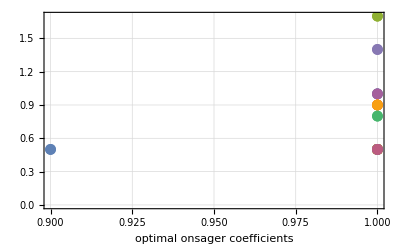

```mathematica
ListPlot[OptimalCoeffsKn0p1,GridLines->Automatic,Frame->True,FrameLabel->{"optimal onsager coefficients"}]
```

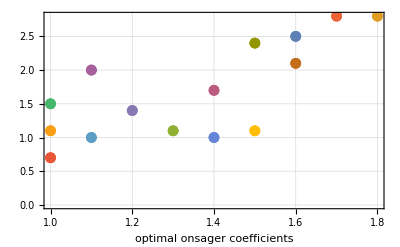

```mathematica
ListPlot[OptimalCoeffsKn1p0,GridLines->Automatic,Frame->True,FrameLabel->{"optimal onsager coefficients"}]
```

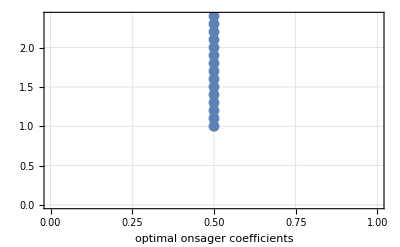

```mathematica
ListPlot[OptimalCoeffsKn10p0,GridLines->Automatic,Frame->True,FrameLabel->{"optimal onsager coefficients"}]
```

### Write Optimal error and Onsager Coefficients

#### Kn = 0.1

```mathematica
Do[WriteError[resultPBCOptKn0p1[ii],"Kn0p1/OptimalError",ii],{ii,min,max}];
```

#### Kn = 1.0

```mathematica
Do[WriteError[resultPBCOptKn1p0[ii],"Kn1p0/OptimalError",ii],{ii,min,max}];
```

#### Kn = 10.0

```mathematica
Do[WriteError[resultPBCOptKn10p0[ii][x],"Kn10p0/OptimalError",ii],{ii,min,max}];
```

## Results Accelerated

### Kn = 0.1

#### averaged

```mathematica
AvgKn0p1 = ReturnErrorAvg[min,max,0.1,HighOrderKn0p1];
```

Obtained solution

Computing error for Kn = 0.1

{0.00666602,0.00440552,0.00354377,0.0034816,0.00281169,0.00284903,0.00239942,0.0024027,0.0020879,0.00207491,0.00184562,0.0018254,0.00165264,0.00162975,0.00149581}

#### accelerated

```mathematica
AccKn0p1 =  ReturnErrorAcc[min,max,0.1,HighOrderKn0p1]
```

Obtained solution

Computing error for Kn = 0.1

{0.00666602,0.00504433,0.00426377,0.0038767,0.00367544,0.00349083,0.00332148,0.0031659,0.00302271,0.00289068,0.00276871,0.00265583,0.00255114,0.00245387,0.00236333}

### Kn = 1.0

#### averaged

```mathematica
AvgKn1p0 = ReturnErrorAvg[min,max,1.0,HighOrderKn1p0]
```

Obtained solution

Computing error for Kn = 1.0

{0.038961,0.0479452,0.0401386,0.0423638,0.0371229,0.0381469,0.0342488,0.0348195,0.0317637,0.0321126,0.0296356,0.0298597,0.0278034,0.0279508,0.0262128}

#### accelerated

```mathematica
AccKn1p0 =  ReturnErrorAcc[min,max,1.0,HighOrderKn1p0]
```

Obtained solution

Computing error for Kn = 1.0

{0.038961,0.0434531,0.0437475,0.043197,0.0423844,0.0414835,0.0405619,0.0396498,0.0387613,0.0379031,0.037078,0.0362866,0.0355284,0.0348026,0.0341077}

### Kn = 10.0

#### averaged

```mathematica
AvgKn10p0 = ReturnErrorAvg[min,max,10.0,HighOrderKn10p0]
```

Obtained solution

Computing error for Kn = 10.0

{0.0210633,0.0224499,0.0209432,0.0212554,0.0201373,0.0202635,0.0193547,0.0194134,0.0186414,0.0186686,0.0179949,0.0180055,0.0174066,0.0174077,0.016868}

#### accelerated

```mathematica
AccKn10p0 =  ReturnErrorAcc[min,max,10.0,HighOrderKn10p0]
```

Obtained solution

Computing error for Kn = 10.0

{0.0210633,0.0217566,0.0217266,0.0215622,0.0213551,0.0211328,0.0209065,0.0206812,0.0204595,0.0202425,0.0200308,0.0198247,0.0196241,0.0194291,0.0192394}

### Plots

#### plotting routine

```mathematica
PlotErrorAcc[error_,Kn_]:=Module[{numvariations,ptlegends,TicksXAxis,legendfont},

(*Number of variations which we allow in the plot*)
numvariations=Length[error];
If[numvariations==1,Print[Style["Not Implemeneted",FontColor->Red]]];

legendfont = 16;
ptlegends={Style["Averaged Solution",FontSize->legendfont],Style["Euler's Transform",FontSize->legendfont]};

TicksXAxis = Table[{ii-min+1,ii},{ii,min,max,1}];

ListPlot[error,Frame->True,GridLines->Automatic,FrameLabel->{{Style["errorθ",FontSize->16],None},{Style["m",FontSize->16],None}},FrameTicks->{{Automatic,None},{TicksXAxis,None}},ImageSize->600,Joined->True,PlotMarkers->{Graphics[{Red,Thick,Circle[]},ImageSize->14],Graphics[{Green,Thick,Circle[]},ImageSize->10],
Graphics[{Blue,Thick,Circle[]},ImageSize->10]},PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}},PlotLegends->Placed[{ptlegends},{0.8,0.9}],FrameTicksStyle->{{Directive[FontSize->13,Black],None},{Directive[FontSize->13,{Orange,Black}],None}}]

]
```

#### Kn = 0.1

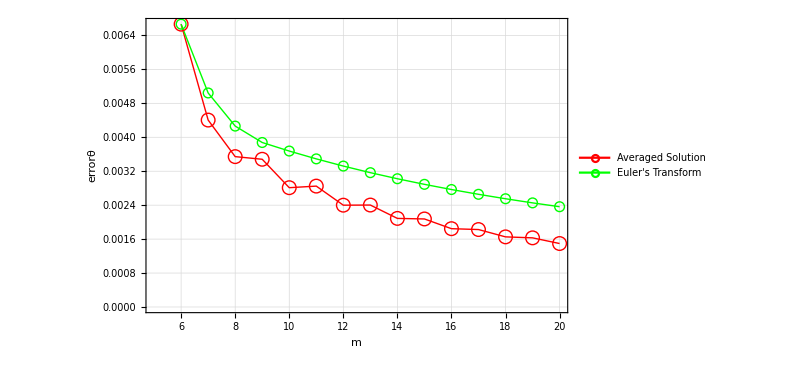

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Accelerated_Convergence/Kn0p1/error_theta.eps

```mathematica
plt=PlotErrorAcc[{AvgKn0p1,AccKn0p1},0.1]
Export[StringJoin[WriteDirectoryResults,"Accelerated_Convergence/Kn0p1/","error_theta.eps"],plt]
```

#### Kn = 1.0

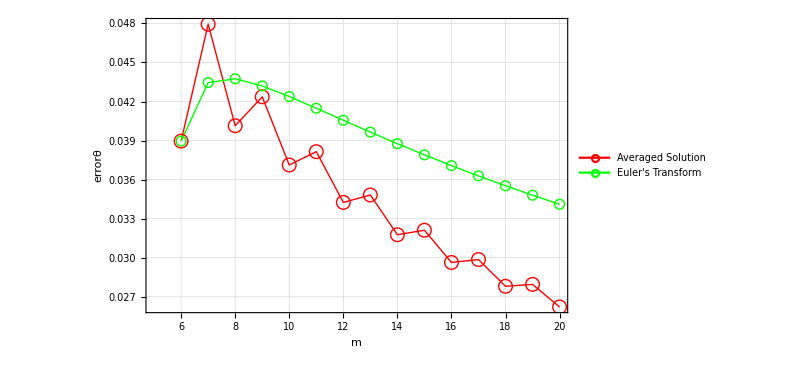

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Accelerated_Convergence/Kn1p0/error_theta.eps

```mathematica
plt=PlotErrorAcc[{AvgKn1p0,AccKn1p0},0.1]

Export[StringJoin[WriteDirectoryResults,"Accelerated_Convergence/Kn1p0/","error_theta.eps"],plt]
```

#### Kn = 10.0

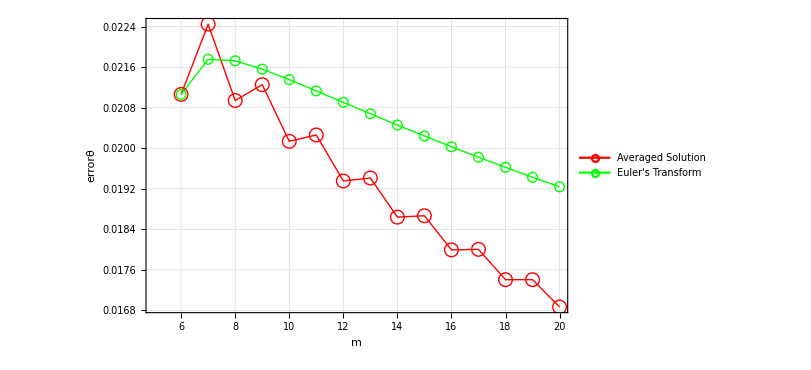

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Accelerated_Convergence/Kn10p0/error_theta.eps

```mathematica
plt=PlotErrorAcc[{AvgKn10p0,AccKn10p0},10.0]
Export[StringJoin[WriteDirectoryResults,"Accelerated_Convergence/Kn10p0/","error_theta.eps"],plt]
```